# Scalar annihilation into gravitons in Einstein–scalar–Gauss–Bonnet theory

Tree-level p1 + p2 → p3 + p4, with two incoming real scalars of mass m and two outgoing massless gravitons. The additional interaction is (g1 phi + g2 phi^2/2) times the Gauss–Bonnet invariant. Both couplings are independent. Start in a fresh kernel and evaluate from top to bottom. This example follows the native FeynArts workflow of examples 09 and 10; it computes a polarisation-dependent amplitude, not a spin sum or cross section.

The minimal two-graviton scalar contact has been corrected. Both graviton Ward identities now vanish for the rebuilt model with symbolic D, mass and couplings. Start in a fresh kernel so FeynArts loads the corrected model. The checks below act on the tensor amplitude before inserting helicities. See Documentation/Verification/ScalarWardCorrection.md.

## 1. Load FeynGrav

```mathematica
$LoadAddOns = {"FeynArts"};
<<"FeynGrav`";
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.1

Feynman rules for gravity and matter, with FeynCalc notation and FORM support through CalcFormConverter.

The default libraries include cubic and quartic graviton vertices and scalar, Dirac fermion and vector interactions with up to two gravitons. Use the FeynGravImport* commands to load additional libraries.

FeynArts supported models

• Pure general relativity

• Scalar field with a potential minimally coupled to gravity

• Scalar field with a non-minimal kinetic coupling

• Einstein-scalar-Gauss-Bonnet model

The supplied models retain interactions through order κ^2 per vertex. Use matching Model and GenericModel names with FeynCalc-patched FeynArts in a fresh kernel. Models are not initialised automatically.

Evaluate FeynGravCommands[] to list available commands, FeynGravConventions[] to inspect conventions and current settings, and FeynGravHowToCite[] for citation guidance.

## 2. Load the FeynArts model

```mathematica
model = "Einstein-scalar-Gauss-Bonnet";
```

## 3. Generate and display the diagrams

Six diagrams contribute: the combined minimal/Gauss–Bonnet hh phi phi contact; the minimal s-channel graviton exchange; minimal t- and u-channel scalar exchanges; and two additional t- and u-channel graviton exchanges proportional to g1^2. Ghosts do not contribute to this tree. The last two diagrams have total order kappa^4; they are retained because the model cutoff is kappa^2 per vertex, not per amplitude.

```mathematica
topologies = CreateTopologies[0, 2 -> 2, Adjacencies -> {3, 4}];
insertions = InsertFields[topologies, {S[1], S[1]} -> {T[1], T[1]}, Model -> model, GenericModel -> model, InsertionLevel -> {Classes}];
```

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/Einstein-scalar-Gauss-Bonnet/Einstein-scalar-Gauss-Bonnet.gen

> $GenericMixing is OFF

generic model {Einstein-scalar-Gauss-Bonnet} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/Einstein-scalar-Gauss-Bonnet/Einstein-scalar-Gauss-Bonnet.mod

> 4 particles (incl. antiparticles) in 3 classes

> $CounterTerms are ON

> 6 vertices

classes model {Einstein-scalar-Gauss-Bonnet} initialized

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 2 Classes insertions

> Top. 4: 2 Classes insertions

in total: 6 Classes insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

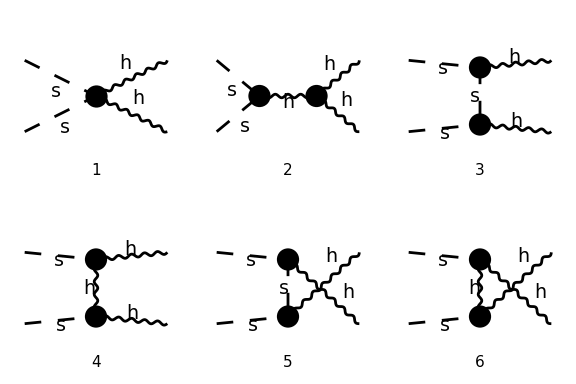

```mathematica
Paint[insertions, ColumnsXRows -> {3, 2}, Numbering -> Simple, SheetHeader -> "Scalar annihilation into gravitons: Einstein–scalar–Gauss–Bonnet", DisplayFunction -> (Print /@ Render[#, ImageSize -> {576, 384}] &)];
```

## 4. Fix the on-shell kinematics and external polarisations

p1 and p2 are incoming scalar momenta; p3 and p4 are outgoing graviton momenta. Thus p1 + p2 = p3 + p4 and s + t + u = 2 m^2. SetMandelstam receives all-incoming momenta. All tensors and scalar products retain symbolic D; no D -> 4 limit is taken. Generic physical scattering has s > 4 m^2.

```mathematica
FCClearScalarProducts[];
SetMandelstam[s, t, u, p1, p2, -p3, -p4, m, m, 0, 0];
```

The following scalar products choose outgoing helicities H3 = 2 h3 and H4 = 2 h4, with h3,h4 = ±1, in a four-dimensional centre-of-mass external-state subspace. The argument -I selects conjugated outgoing polarisations; it is not a helicity label. The tensors and contractions retain symbolic D: these two helicities are not a complete D-dimensional polarisation sum. The chosen vectors are null and transverse, with the phases fixed by the scalar-product table below. A vector dotted with itself is different from its product with its complex conjugate.

```mathematica
Pair[Momentum[Polarization[p3,-I],D],Momentum[Polarization[p3,-I],D]]=0;
Pair[Momentum[Polarization[p4,-I],D],Momentum[Polarization[p4,-I],D]]=0;
Pair[Momentum[Polarization[p3,-I],D],Momentum[Polarization[p4,-I],D]]=-(1+h3 h4)/2;
```

```mathematica
Pair[Momentum[p1,D],Momentum[Polarization[p3,-I],D]]=-ⅈ h3 √((t u -m^4)/(2 s));
Pair[Momentum[p2,D],Momentum[Polarization[p3,-I],D]]=+ⅈ h3 √((t u -m^4)/(2 s));
Pair[Momentum[p3,D],Momentum[Polarization[p3,-I],D]]=0;
Pair[Momentum[p4,D],Momentum[Polarization[p3,-I],D]]=0;
```

```mathematica
Pair[Momentum[p1,D],Momentum[Polarization[p4,-I],D]]=+ⅈ h4 √((t u -m^4)/(2 s));
Pair[Momentum[p2,D],Momentum[Polarization[p4,-I],D]]=-ⅈ h4 √((t u -m^4)/(2 s));
Pair[Momentum[p3,D],Momentum[Polarization[p4,-I],D]]=0;
Pair[Momentum[p4,D],Momentum[Polarization[p4,-I],D]]=0;
```

```mathematica
Contract[FVD[p2,σ]PolarizationVectorD[p3,σ,-ⅈ]]=Contract[FVD[p4,σ]PolarizationVectorD[p3,σ,-ⅈ]-FVD[p1,σ]PolarizationVectorD[p3,σ,-ⅈ]];
Contract[FVD[p2,σ]PolarizationVectorD[p4,σ,-ⅈ]]=Contract[FVD[p3,σ]PolarizationVectorD[p4,σ,-ⅈ]-FVD[p1,σ]PolarizationVectorD[p4,σ,-ⅈ]];
```

```mathematica
$Assumptions=h3^2==1&&h4^2==1;
```

```mathematica
externalTensors =PolarizationTensorD[p3, μ3, ν3,-ⅈ]PolarizationTensorD[p4, μ4, ν4,-ⅈ];
```

## 5. Calculate the on-shell amplitude

The diagram result is i M; division by I defines M. External propagators are removed and the two outgoing polarisation tensors are attached explicitly. ScalarMass, GaussBonnetG1 and GaussBonnetG2 are replaced by m, g1 and g2. The option ChangeDimension -> D keeps the converted tensors in the same Lorentz space as the external polarisations; explicit D-dependent coefficients are retained. No loop integration, symmetry factor for final-state phase space or polarisation sum is performed.

```mathematica
ℳ = Collect[Simplify[ExpandScalarProduct[Contract[FeynAmpDenominatorExplicit[FCFAConvert[CreateFeynAmp[insertions, PreFactor -> 1, GaugeRules -> {}, MomentumConservation -> True, Truncated -> True], IncomingMomenta -> {p1, p2}, OutgoingMomenta -> {p3, p4}, LorentzIndexNames -> {μ3, ν3, μ4, ν4, α, β, γ, δ},  ChangeDimension -> D, Contract -> False, List -> False, Prefactor -> 1] /. {ScalarMass -> m, GaussBonnetG1 -> g1, GaussBonnetG2 -> g2}] externalTensors]]/I ], {g1, g2}, Factor];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 2 Classes amplitudes

> Top. 4: 2 Classes amplitudes

in total: 6 Classes amplitudes

Gauge invariance must be checked on the tensor amplitude, not by replacing polarisations in the final helicity expression. Here ξ is arbitrary and the other graviton is represented by a generic transverse null vector ε3 or ε4. Crossed products ε3·p4 and ε4·p3 are not set to zero. Symmetry supplies the other term in the gauge variation pμ ξν + ξμ pν. The expected residuals are {0, 0}.

```mathematica
wardTensor = FeynAmpDenominatorExplicit[FCFAConvert[CreateFeynAmp[insertions, PreFactor -> 1, GaugeRules -> {}, MomentumConservation -> True, Truncated -> True], IncomingMomenta -> {p1, p2}, OutgoingMomenta -> {p3, p4}, LorentzIndexNames -> {μ3, ν3, μ4, ν4, α, β, γ, δ}, ChangeDimension -> D, Contract -> False, List -> False, Prefactor -> 1] /. {ScalarMass -> m, GaussBonnetG1 -> g1, GaussBonnetG2 -> g2}]/I;
wardRules = FCI[{SPD[ε3] -> 0, SPD[ε4] -> 0, SPD[ε3, p3] -> 0, SPD[ε4, p4] -> 0, SPD[ε3, p2] -> SPD[ε3, p4] - SPD[ε3, p1], SPD[ε4, p2] -> SPD[ε4, p3] - SPD[ε4, p1], SPD[ξ, p2] -> SPD[ξ, p3] + SPD[ξ, p4] - SPD[ξ, p1]}];
wardResiduals = (Factor[Together[ExpandScalarProduct[Contract[wardTensor #]] /. wardRules /. u -> 2 m^2 - s - t]] &) /@ {FVD[p3, μ3] FVD[ξ, ν3] FVD[ε4, μ4] FVD[ε4, ν4], FVD[ε3, μ3] FVD[ε3, ν3] FVD[p4, μ4] FVD[ξ, ν4]};
wardResiduals
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 2 Classes amplitudes

> Top. 4: 2 Classes amplitudes

in total: 6 Classes amplitudes

{0,0}

## 6. Present the amplitude

```mathematica
mMinimal = ℳ /. {g1 -> 0, g2 -> 0};
mQuadraticCoupling = g2 Coefficient[ℳ, g2, 1];
mLinearCouplingExchange = g1^2 Coefficient[ℳ, g1, 2];
Grid[{{"Contribution to M", "On-shell expression"}, {"Minimal gravity (kappa^2)", TraditionalForm[mMinimal]}, {"g2 contact (kappa^2 g2)", TraditionalForm[mQuadraticCoupling]}, {"Two g1 vertices (kappa^4 g1^2)", TraditionalForm[mLinearCouplingExchange]}}, Frame -> All, Alignment -> Left]
```

Contribution to M | On-shell expression
Minimal gravity (kappa^2) | -1/(16 s^2 (m^2-t) (m^2-u))κ^2 (-10 h3 h4 m^8 s+16 h3 h4 m^6 s t+16 h3 h4 m^6 s u+h3 h4 m^4 s^3-7 h3 h4 m^4 s t^2-22 h3 h4 m^4 s t u-7 h3 h4 m^4 s u^2-h3 h4 m^2 s^3 t-h3 h4 m^2 s^3 u+h3 h4 m^2 s t^3+7 h3 h4 m^2 s t^2 u+7 h3 h4 m^2 s t u^2+h3 h4 m^2 s u^3+h3 h4 s^3 t u-h3 h4 s t^3 u-h3 h4 s t u^3-8 m^10-10 m^8 s+4 m^8 t+4 m^8 u+16 m^6 s t+16 m^6 s u+16 m^6 t u+m^4 s^3-7 m^4 s t^2-22 m^4 s t u-7 m^4 s u^2-8 m^4 t^2 u-8 m^4 t u^2-m^2 s^3 t-m^2 s^3 u+m^2 s t^3+7 m^2 s t^2 u+7 m^2 s t u^2+m^2 s u^3-8 m^2 t^2 u^2+s^3 t u-s t^3 u-s t u^3+4 t^3 u^2+4 t^2 u^3)
g2 contact (kappa^2 g2) | 1/4 g2 κ^2 s^2 (h3 h4+1)
Two g1 vertices (kappa^4 g1^2) | -1/(8 t u)g1^2 κ^4 (3 h3 h4 m^8 t+3 h3 h4 m^8 u-4 h3 h4 m^6 s t-4 h3 h4 m^6 s u-4 h3 h4 m^6 t^2-8 h3 h4 m^6 t u-4 h3 h4 m^6 u^2+h3 h4 m^4 s^2 t+h3 h4 m^4 s^2 u+2 h3 h4 m^4 s t^2+12 h3 h4 m^4 s t u+2 h3 h4 m^4 s u^2+h3 h4 m^4 t^3+5 h3 h4 m^4 t^2 u+5 h3 h4 m^4 t u^2+h3 h4 m^4 u^3-4 h3 h4 m^2 s^2 t u-4 h3 h4 m^2 s t^2 u-4 h3 h4 m^2 s t u^2+h3 h4 s^2 t^2 u+h3 h4 s^2 t u^2-h3 h4 t^3 u^2-h3 h4 t^2 u^3+5 m^8 t+5 m^8 u-4 m^6 s t-4 m^6 s u-4 m^6 t^2-8 m^6 t u-4 m^6 u^2+m^4 s^2 t+m^4 s^2 u+2 m^4 s t^2+12 m^4 s t u+2 m^4 s u^2+m^4 t^3+m^4 t^2 u+m^4 t u^2+m^4 u^3-4 m^2 s^2 t u-4 m^2 s t^2 u-4 m^2 s t u^2+s^2 t^2 u+s^2 t u^2+t^3 u^2+t^2 u^3)

### Consistency checks

The table checks the coupling decomposition, the two generic Ward contractions above and the zero-gravity limit. Equalities are understood away from propagator poles. These tree-level checks do not establish loop results.

```mathematica
kinematicZero[expr_] := Together[ExpandScalarProduct[expr] /. u -> 2 m^2 - s - t] === 0;
checks = {"Coupling decomposition" -> kinematicZero[ℳ - mMinimal - mQuadraticCoupling - mLinearCouplingExchange], "Graviton p3 Ward identity" -> (wardResiduals[[1]] === 0), "Graviton p4 Ward identity" -> (wardResiduals[[2]] === 0), "Gravity switched off" -> kinematicZero[ℳ /. κ -> 0]};
Grid[Prepend[List @@@ checks, {"Check", "Passed"}], Frame -> All, Alignment -> Left]
```

Check | Passed
Coupling decomposition | True
Graviton p3 Ward identity | True
Graviton p4 Ward identity | True
Gravity switched off | True

Specialise m, g1, g2 and h3,h4 by replacement in the amplitude. The graviton helicities are 2 h3 and 2 h4. Use a fresh kernel for another example because scalar-product assignments persist.